```mathematica
qiblas={{Qibla, City, Country}, {"Petra", "Wadi Musa", "Jordan"}, {"Kaāba", "Mecca", "SaudiArabia"}, {"al-Aqsa", "Jerusalem", "Israel"}}   ;
```

```mathematica
direction=GeoDirection@@Map[#~CityData~"Coordinates"&,{##}]&;
```

```mathematica
compareQibla[city_, orientation_ : 0] := Module[
{a, o=Point@{0,0}, g={Red,Green,Blue,Gray}, q},
a=Arrow@AnglePath[{π/2-#}]&;
q=Riffle[g,First/@qiblas];
g=Riffle[g,a@direction[city,Rest@#]&/@qiblas];
If[orientation!=0,o=a[orientation];q~AppendTo~"Mosque Orientation"];
g=Graphics[{Thick,Sequence@@g,o,Dashed,Thickness@Medium,Circle[]},
ImageSize->Medium,PlotLabel->city~StringRiffle~", "];
Row@{g, LineLegend@@Thread@Partition[q,2]}]
```

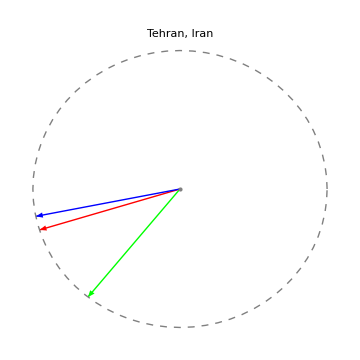

```mathematica
compareQibla[{"Tehran","Iran"}]
```

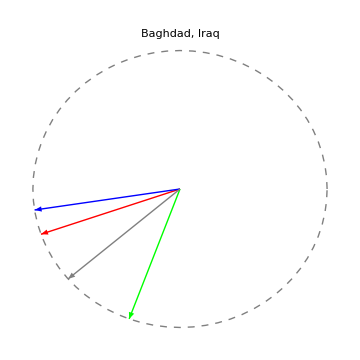

```mathematica
compareQibla[{"Baghdad","Iraq"},229.5°]
```